# Elemento Isoparamétrico de 4 Nodos

## Ing. Jorge De La Cruz. M.Sc. Análisis por medio del Método de Elementos Finitos.

## Resumen

En el presente trabajo se presenta la implementación de un elemento cuadrilátero bilineal de 4 nodos a través de una formulación isoparamétrica. La configuración del elemento en el espacio (x, y) es repesentada en el espacio de  las coordenadas naturales (ξ ,η) , se establecen las relaciones entre las derivadas de las funciones de forma respecto a las coordenadas espaciales (x,y)   y las coordenadas naturales. Y por último la matriz de rigidez es calculada utilizando cuadratura Gaussiana para la geometría del elemento presentado a la vez que se asume un comportamiento elástico lineal bajo el estado de tensión plana.

## Geometría del Elemento

Como el título lo indica, en este trabajo se presenta la implementación de un elemento cuadrilátero bilinial de 4 nodos. En principio el elemento puede tener una forma cuadrada o rectangular como se muestra en la figura 1, pero también  podría taner una forma irregular como la mostrada en la figura 2.

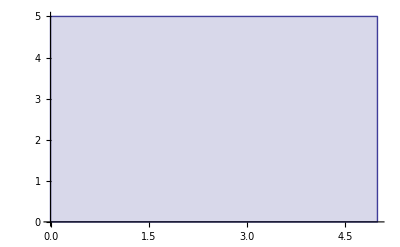

```mathematica
x1=0.0; y1=0.0;
x2=5.0; y2=0.0;
x3=5.0; y3=5.0;
x4=0.0; y4=5.0;
ListLinePlot[{{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x1,y1}},Filling->Bottom]
```

Figura 1: Elemento cuadrilátero rectangular.

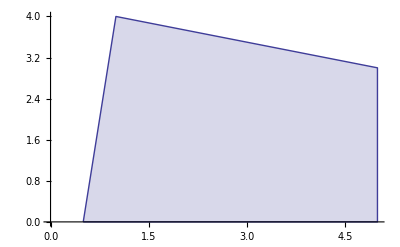

```mathematica
x1=0.5; y1=0.0;
x2=5.0; y2=0.0;
x3=5.0; y3=3.0;
x4=1.0; y4=4.0;
ListLinePlot[{{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x1,y1}},Filling->Bottom]
```

Figura 2: Elemento cuadrilátero irregular.

La diferencia fundamental entre los dos tipos de elementos se presenta a la hora de realizar la integral (1) y obtener la matriz de rigidez. En el primero la integral tiene solución analítica mientras que en el segundo caso la integral tiene que ser resuelta  de forma numérica, es frecuente utilizar cuadratura gaussiana para resolver dicha integral.

K^e=∫_-1^1 ∫_-1^1 B^T D B|J|ⅆηⅆξ

En este caso se utiliza un elemento cuadrilatero irregular como el que se muestra en la figura 2. Las coordenadas de los nodos de este elemento son:

```mathematica
x1=0.5; y1=0.0;
x2=5.0; y2=0.0;
x3=5.0; y3=3.0;
x4=1.0; y4=4.0;
```

Las funciones  de forma utilizadas para representar el campo de desplazamiento en el espacio (ξ,η) y que satisfacen la condición de que la función tenga el valor de la unidad sólo en el nodo que representa y cero en el resto son:

```mathematica
N1=1/4(1-ξ)(1-η);
N2=1/4(1+ξ)(1-η);
N3=1/4(1+ξ)(1+η);
N4=1/4(1-ξ)(1+η);
```

Si graficamos las funciones de forma  se puede ver como la función de forma sólo tiene un valor de 1 en el nodo al cual representa y cero en los otros, la interpolación entre este nodo y el resto es lineal como se puede observar en la figura 2. En la figura 4 se representan las funciones de interpolación utilizadas en elmento cuadrilátero.

```mathematica
Plot3D[N1,{ξ,-1,1},{η,-1,1}]
```

-Graphics3D-

Figura 3: Representación de una de las funciones de forma

```mathematica
Plot3D[{N1,N2,N3,N4},{ξ,-1,1},{η,-1,1}]
```

-Graphics3D-

Figura 4: Representación de las 4 funciones de forma.

Podemos realizar el mapeado del espacio (ξ,η) al (x,y) utilizando las funciones de forma (N1, N2, N3, N4) de un elemento de 4 nodos, obteniendo  las funciones  x(ξ,η) y y(ξ,η) presentadas en las ecuaciones (2) y (3) respectivamente.

```mathematica
x=Simplify[N1 x1+N2 x2+N3 x3+N4 x4];
y=Simplify[N1 y1+N2 y2+N3 y3+N4 y4];
```

x=2.875+η (0.125-0.125 ξ)+2.125 ξ

y=1.75+η (1.75-0.25 ξ)-0.25 ξ

Ahora obtenemos el jacobiano de la transformación:

```mathematica
(Jmat={{D[x,ξ],D[x,η]},{D[y,ξ],D[y,η]}})//MatrixForm
```

(2.125-0.125 η | 0.125-0.125 ξ
-0.25-0.25 η | 1.75-0.25 ξ)

Luego calculamos el determinante del Jacobiano:

```mathematica
jac=Det[Jmat]
```

3.75-0.1875 η-0.5625 ξ

Calculando el gradiente de la función:

```mathematica
(Jinv=Inverse[Jmat])//MatrixForm
```

((1.75-0.25 ξ)/(3.75-0.1875 η-0.5625 ξ) | (-0.125+0.125 ξ)/(3.75-0.1875 η-0.5625 ξ)
(0.25+0.25 η)/(3.75-0.1875 η-0.5625 ξ) | (2.125-0.125 η)/(3.75-0.1875 η-0.5625 ξ))

Por lo tanto ahora tenemos las derivadas inversas:

```mathematica
dξdx=Jinv[[1,1]]
dξdy=Jinv[[1,2]]
dηdx=Jinv[[2,1]]
dηdy=Jinv[[2,2]]
```

(1.75-0.25 ξ)/(3.75-0.1875 η-0.5625 ξ)

(-0.125+0.125 ξ)/(3.75-0.1875 η-0.5625 ξ)

(0.25+0.25 η)/(3.75-0.1875 η-0.5625 ξ)

(2.125-0.125 η)/(3.75-0.1875 η-0.5625 ξ)

Ahora podemos utilizar la regla de la cadena para obtener el gradiente de las funciones de forma:

```mathematica
dN1dx=D[N1,ξ]dξdx+D[N1,η]dηdx
dN1dy=D[N1,ξ]dξdy+D[N1,η]dηdy
```

((-1+η) (1.75-0.25 ξ))/(4 (3.75-0.1875 η-0.5625 ξ))+((0.25+0.25 η) (-1+ξ))/(4 (3.75-0.1875 η-0.5625 ξ))

((-1+η) (-0.125+0.125 ξ))/(4 (3.75-0.1875 η-0.5625 ξ))+((2.125-0.125 η) (-1+ξ))/(4 (3.75-0.1875 η-0.5625 ξ))

```mathematica
dN2dx=D[N2,ξ]dξdx+D[N2,η]dηdx
dN2dy=D[N2,ξ]dξdy+D[N2,η]dηdy
```

((0.25+0.25 η) (-1-ξ))/(4 (3.75-0.1875 η-0.5625 ξ))+((1-η) (1.75-0.25 ξ))/(4 (3.75-0.1875 η-0.5625 ξ))

((2.125-0.125 η) (-1-ξ))/(4 (3.75-0.1875 η-0.5625 ξ))+((1-η) (-0.125+0.125 ξ))/(4 (3.75-0.1875 η-0.5625 ξ))

```mathematica
dN3dx=D[N3,ξ]dξdx+D[N3,η]dηdx
dN3dy=D[N3,ξ]dξdy+D[N3,η]dηdy
```

((1+η) (1.75-0.25 ξ))/(4 (3.75-0.1875 η-0.5625 ξ))+((0.25+0.25 η) (1+ξ))/(4 (3.75-0.1875 η-0.5625 ξ))

((1+η) (-0.125+0.125 ξ))/(4 (3.75-0.1875 η-0.5625 ξ))+((2.125-0.125 η) (1+ξ))/(4 (3.75-0.1875 η-0.5625 ξ))

```mathematica
dN4dx=D[N4,ξ]dξdx+D[N4,η]dηdx
dN4dy=D[N4,ξ]dξdy+D[N4,η]dηdy
```

((0.25+0.25 η) (1-ξ))/(4 (3.75-0.1875 η-0.5625 ξ))+((-1-η) (1.75-0.25 ξ))/(4 (3.75-0.1875 η-0.5625 ξ))

((2.125-0.125 η) (1-ξ))/(4 (3.75-0.1875 η-0.5625 ξ))+((-1-η) (-0.125+0.125 ξ))/(4 (3.75-0.1875 η-0.5625 ξ))

Luego ensamblamos la matriz B (Bmat) la cual esta compuesta por los elementos presentados a continuación :

```mathematica
(Bmat={{dN1dx,0,dN2dx,0,dN3dx,0,dN4dx,0},
{0,dN1dy,0,dN2dy,0,dN3dy,0,dN4dy},
{dN1dy,dN1dx,dN2dy,dN2dx,dN3dy,dN3dx,dN4dy,dN4dx}})//MatrixForm
```

(((-1+η) (1.75-0.25 ξ))/(4 (3.75-0.1875 η-0.5625 ξ))+((0.25+0.25 η) (-1+ξ))/(4 (3.75-0.1875 η-0.5625 ξ)) | 0 | ((0.25+0.25 η) (-1-ξ))/(4 (3.75-0.1875 η-0.5625 ξ))+((1-η) (1.75-0.25 ξ))/(4 (3.75-0.1875 η-0.5625 ξ)) | 0 | ((1+η) (1.75-0.25 ξ))/(4 (3.75-0.1875 η-0.5625 ξ))+((0.25+0.25 η) (1+ξ))/(4 (3.75-0.1875 η-0.5625 ξ)) | 0 | ((0.25+0.25 η) (1-ξ))/(4 (3.75-0.1875 η-0.5625 ξ))+((-1-η) (1.75-0.25 ξ))/(4 (3.75-0.1875 η-0.5625 ξ)) | 0
0 | ((-1+η) (-0.125+0.125 ξ))/(4 (3.75-0.1875 η-0.5625 ξ))+((2.125-0.125 η) (-1+ξ))/(4 (3.75-0.1875 η-0.5625 ξ)) | 0 | ((2.125-0.125 η) (-1-ξ))/(4 (3.75-0.1875 η-0.5625 ξ))+((1-η) (-0.125+0.125 ξ))/(4 (3.75-0.1875 η-0.5625 ξ)) | 0 | ((1+η) (-0.125+0.125 ξ))/(4 (3.75-0.1875 η-0.5625 ξ))+((2.125-0.125 η) (1+ξ))/(4 (3.75-0.1875 η-0.5625 ξ)) | 0 | ((2.125-0.125 η) (1-ξ))/(4 (3.75-0.1875 η-0.5625 ξ))+((-1-η) (-0.125+0.125 ξ))/(4 (3.75-0.1875 η-0.5625 ξ))
((-1+η) (-0.125+0.125 ξ))/(4 (3.75-0.1875 η-0.5625 ξ))+((2.125-0.125 η) (-1+ξ))/(4 (3.75-0.1875 η-0.5625 ξ)) | ((-1+η) (1.75-0.25 ξ))/(4 (3.75-0.1875 η-0.5625 ξ))+((0.25+0.25 η) (-1+ξ))/(4 (3.75-0.1875 η-0.5625 ξ)) | ((2.125-0.125 η) (-1-ξ))/(4 (3.75-0.1875 η-0.5625 ξ))+((1-η) (-0.125+0.125 ξ))/(4 (3.75-0.1875 η-0.5625 ξ)) | ((0.25+0.25 η) (-1-ξ))/(4 (3.75-0.1875 η-0.5625 ξ))+((1-η) (1.75-0.25 ξ))/(4 (3.75-0.1875 η-0.5625 ξ)) | ((1+η) (-0.125+0.125 ξ))/(4 (3.75-0.1875 η-0.5625 ξ))+((2.125-0.125 η) (1+ξ))/(4 (3.75-0.1875 η-0.5625 ξ)) | ((1+η) (1.75-0.25 ξ))/(4 (3.75-0.1875 η-0.5625 ξ))+((0.25+0.25 η) (1+ξ))/(4 (3.75-0.1875 η-0.5625 ξ)) | ((2.125-0.125 η) (1-ξ))/(4 (3.75-0.1875 η-0.5625 ξ))+((-1-η) (-0.125+0.125 ξ))/(4 (3.75-0.1875 η-0.5625 ξ)) | ((0.25+0.25 η) (1-ξ))/(4 (3.75-0.1875 η-0.5625 ξ))+((-1-η) (1.75-0.25 ξ))/(4 (3.75-0.1875 η-0.5625 ξ)))

Para continuar con los calculos supondremos un material con módulo de elasticidad (Y) de 10M y un coeficiente de Poisson (ν) de 0.33. Y siendo la matriz Cmat la matriz que representa la ley constitutiva del material elástico lineal sometido a tensión plana.

```mathematica
ν=0.33;
Y=10.0*10^6;
(Cmat=Y/(1-ν^2){{1,ν,0},{ν,1,0},{0,0,(1-ν)/2}})//MatrixForm
```

(1.12221×10^7 | 3.70329×10^6 | 0.
3.70329×10^6 | 1.12221×10^7 | 0.
0. | 0. | 3.7594×10^6)

La integración de la ecuación (1) se realiza utilizando dos puntos de integración de Gauss (q1,w1)  y (q2,w2) presentados a continuación:

```mathematica
q1=-0.5773502691;q2=-q1;w1=1.0;w2=1.0;
intg=(Transpose[Bmat].Cmat.Bmat)jac;
```

Luego de realizar la multiplicación de los términos dentro de la integral (1) se procede a resolver la integral obteniendo la matriz de rigidez elemental ke. Matriz la cual tiene dimensiones de 8x8.

```mathematica
(ke=(intg w1 w1/.{ξ->q1,η->q1})+(intg w1 w2/.{ξ->q1,η->q2})+
(intg w2 w1/.{ξ->q2,η->q1})+(intg w2 w2/.{ξ->q2,η->q2}))//MatrixForm
```

(4.74291×10^6 | 2.02549×10^6 | -2.14488×10^6 | 310381. | -2.8733×10^6 | -1.93689×10^6 | 275274. | -398973.
2.02549×10^6 | 4.89266×10^6 | 338436. | 1.38055×10^6 | -1.93689×10^6 | -2.64867×10^6 | -427029. | -3.62454×10^6
-2.14488×10^6 | 338436. | 4.366×10^6 | -1.61211×10^6 | -425830. | -460251. | -1.79529×10^6 | 1.73392×10^6
310381. | 1.38055×10^6 | -1.61211×10^6 | 6.04838×10^6 | -432196. | -4.46604×10^6 | 1.73392×10^6 | -2.96289×10^6
-2.8733×10^6 | -1.93689×10^6 | -425830. | -432196. | 5.67771×10^6 | 2.06978×10^6 | -2.37858×10^6 | 299307.
-1.93689×10^6 | -2.64867×10^6 | -460251. | -4.46604×10^6 | 2.06978×10^6 | 6.01465×10^6 | 327362. | 1.10005×10^6
275274. | -427029. | -1.79529×10^6 | 1.73392×10^6 | -2.37858×10^6 | 327362. | 3.8986×10^6 | -1.63425×10^6
-398973. | -3.62454×10^6 | 1.73392×10^6 | -2.96289×10^6 | 299307. | 1.10005×10^6 | -1.63425×10^6 | 5.48738×10^6)

## Conclusiones

Se implementó un elemento cuadrilatero bilineal sometido a un estado de tensión plana, generando como resultado un código capaz de obtener en Mathematica la matriz de rigidez elemental para un elemento cuadrilatero de 4 nodos regular o irregular. Este código es posible utilizarlo como base para el desarrollo de  algoritmos orientados a resolver problemas concretos de tensión plana utilizando elementos cuadriláteros como parte de los mallados utilizados.

# Implementación de un elemento Q4:

Definiendo las coordenadas de los nodos de la malla:

```mathematica
ClearAll["Global`*"]
dir="/Users/jorgedelacruz/Dropbox/Google Drive/Mathematica";
Get["EQ4.m",Path->dir]
```

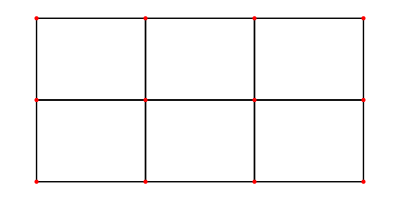

```mathematica
MallaQ4[4,3,10.,5.]
```

Cálculo de las matrices de rigidez elementales:

```mathematica
p0={{0.,0.},{3.,1.},{5,0.5},{10.,0.},{0.,5.},{3.,4.},{6,4.5},{10.,5.},{0.0,9.0},{4.0,8.5},{6.0,9.0},{10.0,9.0}};
GlobalMK[p0];
GlobalK//MatrixForm;
GlobalK-Transpose[GlobalK];
MBDBe[[1]]//MatrixForm;
```

```mathematica
GlobalKAmp=Array[0&,{2 NNodos,4 NNodos}];
GlobalKAmp[[{1,12}]]//MatrixForm;
For[i=1,i<(2 NNodos+1),i++,(
For[j=1,j<(2 NNodos+1),j++,(
GlobalKAmp[[i,j]]=GlobalK[[i,j]]
)]
)]
For[i=1,i<(2 NNodos+1),i++,(
GlobalKAmp[[i,i+2 NNodos]]=1;
)]
GlobalKAmp//MatrixForm;
Dimensions[GlobalKAmp];
VecIn=Array[0&,{4 NNodos}];
DeltaU=Array[0&,{ NNodos,2}]
```

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

Ahora se especifican las condiones de contorno del problema dentro del vector VecIn:

```mathematica
VecIn[[7]]=4.0;VecIn[[15]]=4.0;VecIn[[23]]=4.0;
VecIn[[3]]=u2x;VecIn[[4]]=u2y;VecIn[[5]]=u3x;VecIn[[6]]=u3y;VecIn[[11]]=u6x;VecIn[[12]]=u6y;VecIn[[13]]=u7x;VecIn[[14]]=u7y;VecIn[[19]]=u10x;VecIn[[20]]=u10y;VecIn[[21]]=u11x;VecIn[[22]]=u11y;
```

Ahora se especifican las fuerzas:

```mathematica
VecIn[[25]]=f1x;VecIn[[26]]=f1y;VecIn[[31]]=f4x;VecIn[[32]]=f4y;VecIn[[33]]=f5x;VecIn[[34]]=f5y;VecIn[[39]]=f8x;VecIn[[40]]=f8y;VecIn[[41]]=f9x;VecIn[[42]]=f9y;VecIn[[47]]=f12x;VecIn[[48]]=f12y;
```

```mathematica
Solucion=GlobalKAmp.VecIn;
Dimensions[Solucion];
Solucion=NSolve[{Solucion[[2]]==0 , Solucion[[1]]==0 ,Solucion[[3]]==0,Solucion[[4]]==0,Solucion[[5]]==0
,Solucion[[6]]==0,Solucion[[7]]==0 ,Solucion[[9]]==0 ,Solucion[[8]]==0 ,Solucion[[10]]==0
,Solucion[[11]]==0,Solucion[[12]]==0,Solucion[[13]]==0,Solucion[[14]]==0 ,Solucion[[15]]==0 ,Solucion[[16]]==0  ,Solucion[[17]]==0 ,Solucion[[18]]==0 ,Solucion[[19]]==0,Solucion[[20]]==0,Solucion[[21]]==0,Solucion[[22]]==0 ,Solucion[[23]]==0 ,Solucion[[24]]==0    },{u2x,u2y,u3x,u3y,u6x,u6y,u7x,u7y,u10x,u10y,u11x,u11y,f1x,f1y,f4x,f4y,f5x,f5y,f8x,f8y,f9x,f9y,f12x,f12y}]
VecIn
Dimensions[VecIn]
```

{{u2x→1.20433,u2y→0.471411,u3x→2.17804,u3y→0.617878,u6x→1.14647,u6y→0.0702844,u7x→2.45637,u7y→-0.0109028,u10x→1.65545,u10y→-0.550614,u11x→2.47734,u11y→-0.617936,f1x→8.97266×10^6,f1y→2.38663×10^6,f4x→-9.58948×10^6,f4y→2.97462×10^6,f5x→1.80409×10^7,f5y→87594.9,f8x→-1.69089×10^7,f8y→-258217.,f9x→8.1489×10^6,f9y→-2.57655×10^6,f12x→-8.6641×10^6,f12y→-2.61407×10^6}}

{0,0,u2x,u2y,u3x,u3y,4.,0,0,0,u6x,u6y,u7x,u7y,4.,0,0,0,u10x,u10y,u11x,u11y,4.,0,f1x,f1y,0,0,0,0,f4x,f4y,f5x,f5y,0,0,0,0,f8x,f8y,f9x,f9y,0,0,0,0,f12x,f12y}

{48}

```mathematica
Module[{j,i},(
i=1;
For[j=1,j<( 2 NNodos),j=j+2,(
DeltaU[[i,1]]=VecIn[[j]];
i++;
)];
i=1;
For[j=2,j<(2  NNodos+1),j=j+2,(
DeltaU[[i,2]]=VecIn[[j]];
i++;
)];
)]
DeltaU
VecIn[[3]]
```

{{0,0},{u2x,u2y},{u3x,u3y},{4.,0},{0,0},{u6x,u6y},{u7x,u7y},{4.,0},{0,0},{u10x,u10y},{u11x,u11y},{4.,0}}

u2x

{{0,0},{1.20433,0.471411},{2.17804,0.617878},{4.,0},{0,0},{1.14647,0.0702844},{2.45637,-0.0109028},{4.,0},{0,0},{1.65545,-0.550614},{2.47734,-0.617936},{4.,0}}

{{0.,0.},{4.20433,1.47141},{7.17804,1.11788},{14.,0.},{0.,5.},{4.14647,4.07028},{8.45637,4.4891},{14.,5.},{0.,9.},{5.65545,7.94939},{8.47734,8.38206},{14.,9.}}

{{0.,0.},{3.,1.},{5,0.5},{10.,0.},{0.,5.},{3.,4.},{6,4.5},{10.,5.},{0.,9.},{4.,8.5},{6.,9.},{10.,9.}}

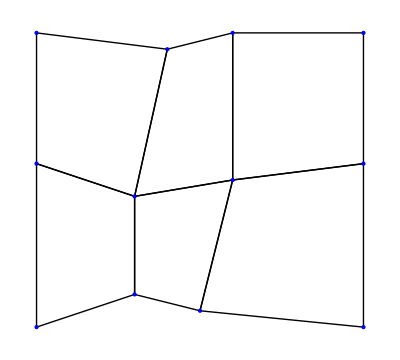

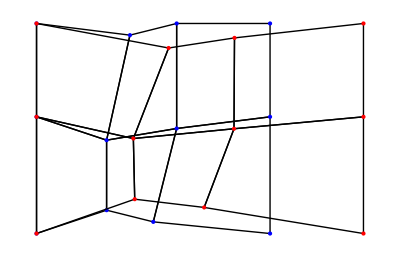

```mathematica
∇U=DeltaU/.First[Solucion]
deformada=p0+∇U
p0
MallaQ42[4,3,p0]
MallaDeform[4,3,p0,deformada]
```

Si ahora aplicamos otro desplazamiento a la configuración deformada:

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

{{u2x→1.10362,u2y→0.326093,u3x→2.25934,u3y→0.408698,u6x→1.14698,u6y→0.0445925,u7x→2.49208,u7y→-0.0178297,u10x→1.59843,u10y→-0.404946,u11x→2.54841,u11y→-0.429146,f1x→5.44233×10^6,f1y→1.92915×10^6,f4x→-5.88624×10^6,f4y→2.40805×10^6,f5x→1.25006×10^7,f5y→132118.,f8x→-1.17232×10^7,f8y→-263497.,f9x→4.84924×10^6,f9y→-2.12453×10^6,f12x→-5.18271×10^6,f12y→-2.0813×10^6}}

{{0,0},{1.10362,0.326093},{2.25934,0.408698},{4.,0},{0,0},{1.14698,0.0445925},{2.49208,-0.0178297},{4.,0},{0,0},{1.59843,-0.404946},{2.54841,-0.429146},{4.,0}}

{{0.,0.},{5.30795,1.7975},{9.43737,1.52658},{18.,0.},{0.,5.},{5.29345,4.11488},{10.9484,4.47127},{18.,5.},{0.,9.},{7.25388,7.54444},{11.0257,7.95292},{18.,9.}}

{{0.,0.},{4.20433,1.47141},{7.17804,1.11788},{14.,0.},{0.,5.},{4.14647,4.07028},{8.45637,4.4891},{14.,5.},{0.,9.},{5.65545,7.94939},{8.47734,8.38206},{14.,9.}}

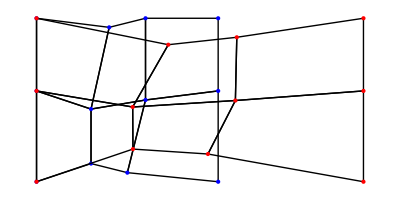

```mathematica
pref=p0;
p0=deformada;
GlobalMK[p0];
GlobalKAmp=Array[0&,{2 NNodos,4 NNodos}];
GlobalKAmp[[{1,12}]]//MatrixForm;
For[i=1,i<(2 NNodos+1),i++,(
For[j=1,j<(2 NNodos+1),j++,(
GlobalKAmp[[i,j]]=GlobalK[[i,j]]
)]
)]
For[i=1,i<(2 NNodos+1),i++,(
GlobalKAmp[[i,i+2 NNodos]]=1;
)]
GlobalKAmp//MatrixForm;
Dimensions[GlobalKAmp];
VecIn=Array[0&,{4 NNodos}];
DeltaU=Array[0&,{ NNodos,2}]

VecIn[[7]]=4.0;VecIn[[15]]=4.0;VecIn[[23]]=4.0;
VecIn[[3]]=u2x;VecIn[[4]]=u2y;VecIn[[5]]=u3x;VecIn[[6]]=u3y;VecIn[[11]]=u6x;VecIn[[12]]=u6y;VecIn[[13]]=u7x;VecIn[[14]]=u7y;VecIn[[19]]=u10x;VecIn[[20]]=u10y;VecIn[[21]]=u11x;VecIn[[22]]=u11y;

VecIn[[25]]=f1x;VecIn[[26]]=f1y;VecIn[[31]]=f4x;VecIn[[32]]=f4y;VecIn[[33]]=f5x;VecIn[[34]]=f5y;VecIn[[39]]=f8x;VecIn[[40]]=f8y;VecIn[[41]]=f9x;VecIn[[42]]=f9y;VecIn[[47]]=f12x;VecIn[[48]]=f12y;

Solucion=GlobalKAmp.VecIn;
Dimensions[Solucion];
Solucion=NSolve[{Solucion[[2]]==0 , Solucion[[1]]==0 ,Solucion[[3]]==0,Solucion[[4]]==0,Solucion[[5]]==0
,Solucion[[6]]==0,Solucion[[7]]==0 ,Solucion[[9]]==0 ,Solucion[[8]]==0 ,Solucion[[10]]==0
,Solucion[[11]]==0,Solucion[[12]]==0,Solucion[[13]]==0,Solucion[[14]]==0 ,Solucion[[15]]==0 ,Solucion[[16]]==0  ,Solucion[[17]]==0 ,Solucion[[18]]==0 ,Solucion[[19]]==0,Solucion[[20]]==0,Solucion[[21]]==0,Solucion[[22]]==0 ,Solucion[[23]]==0 ,Solucion[[24]]==0    },{u2x,u2y,u3x,u3y,u6x,u6y,u7x,u7y,u10x,u10y,u11x,u11y,f1x,f1y,f4x,f4y,f5x,f5y,f8x,f8y,f9x,f9y,f12x,f12y}]

Module[{j,i},(
i=1;
For[j=1,j<( 2 NNodos),j=j+2,(
DeltaU[[i,1]]=VecIn[[j]];
i++;
)];
i=1;
For[j=2,j<(2  NNodos+1),j=j+2,(
DeltaU[[i,2]]=VecIn[[j]];
i++;
)];
)]

∇U=DeltaU/.First[Solucion]
deformada=p0+∇U
p0
MallaDeform[4,3,pref,deformada]
```

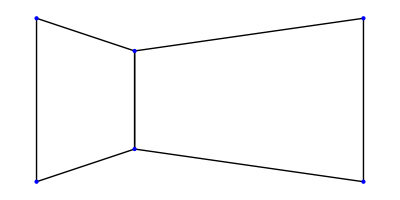

```mathematica
p0={{0.,0.},{3.,1.},{10.,0.},{0.,5.},{3.,4.},{10.,5.}};
p1={{0.,0.},{3.,0.},{10.,0.},
{0.,5.},{3.,4.},{10.,5.},
{0.0,8.0},{4.0,7.0},{10.0,9.0},
{0.0,12.0},{5.0,12.0},{10.0,12.0}};
MallaQ42[3,2,p0]
```

```mathematica
x/d=3
```

Set::write: Tag Times in x/d is Protected.

3

Set::write: Tag Times in d/e is Protected.